## June 25, 2019

### Art of Project Development (Important Notes)

#### Think functionally

Use immutable data

Wolfram data is by default immutable

Helpful for asynchronous programming

Don’t rely on global state

Immutable data are thread safe

Use map and functional constructs instead of imperative constructs

#### Think, design and fail

Before coding think at the outcome

Split your project in components, write down responsibility, write down a pipeline, try to anticipate possible problems and outcomes

Failure is not your enemy

#### Principles and Concepts

Expressions

```mathematica
Quantity[32.82, "USDollars"]
```

```mathematica
Quantity["32.82", "USDollars"]
```

Head and Body

```mathematica
f[x]
```

f[x]

Body may be empty

```mathematica
f[]
```

f[]

Compound Atomic Expressions

Graph

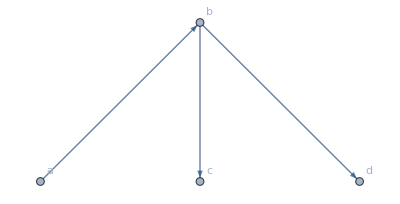

```mathematica
g=Graph[{a->b, b->c, b->d}, VertexLabels->Automatic]
```

Notation Style

FullForm

```mathematica
Plus[2, Times[3,x]]
```

2+3 x

```mathematica
%//FullForm
```

Plus[2,Times[3,x]]

```mathematica
q= 3;
r=4;
s=2;
q^(r-s);
```

Postfix

```mathematica
Map[Cos, {1,2,3}] // Mod[#,3]&
```

{Cos[1],3+Cos[2],3+Cos[3]}

```mathematica
x= RandomInteger[{0,10}, {5,3}] // Grid
```

```mathematica
{{8, 4, 7}, {9, 4, 1}, {2, 3, 5}, {5, 0, 2}, {10, 2, 5}}
```

#### Training for Programmers

Symbols

```mathematica
MatrixForm[{{1,2},{3,4},{5,6}}]
```

(1 | 2
3 | 4
5 | 6)

```mathematica
{{1,2},{3,4}}//MatrixForm
```

(1 | 2
3 | 4)

```mathematica
y = Plus[Times[3,Power[x,2]], Times[2,x],4]
```

4+2 x+3 x^2

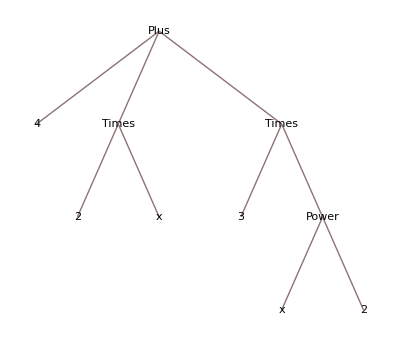

```mathematica
4+2 x+3 x^2
TreeForm[%]
```

```mathematica
Head[x]
```

Symbol

Head of objects themselves are symbols

```mathematica
SymbolName[x]
```

x

```mathematica
Names["Global`*"]
```

{a,b,c,d,expr,f,g,i,Matrix,opts,pi,q,r,s,sol,system,t,t$,uspec,x,X,x$,y}

Pure Functions

```mathematica
Clear[x]
```

```mathematica
Function[# / 2][x]
```

x/2

```mathematica
Function[#1 / 2+ #2][x, 4]
```

4+x/2

```mathematica
Function[{arg1, arg2}, arg1/ 2 + arg2][x,4]
```

4+x/2

## June 26, 2019

### Structured Data

#### List

General objects that represent collections of arbitrary objects


{x,-Graphics3D-,-Graphics-}

```mathematica
{x, Region@Cone[], Plot[Sin[x], {x,0,2Pi}]}
```

MatrixForm is only output style, still just nested list

To extract element, use Part, sort form [[]]

```mathematica
a= List[1,2,3,4,5,6]
```

{1,2,3,4,5,6}

```mathematica
Part[a,2]
```

2

```mathematica
a[[2]]
```

2

Extract/Take can also be used to extract parts from a list

```mathematica
Extract[a,3]
```

3

ReplacePart can also be used to create a new list with parts that have been modified

Flatten converts nested list into an unnested list:

```mathematica
Clear[a,b,c,d,e,f]
```

```mathematica
m1 = {{a,b,c},{d, e, f}}
```

{{a,b,c},{d,e,f}}

```mathematica
m1 // MatrixForm
```

(a | b | c
d | e | f)

```mathematica
Flatten[m1]
```

{a,b,c,d,e,f}

Table can be used to create a list:

```mathematica
Table[i^2,{i, 10}]
```

{1,4,9,16,25,36,49,64,81,100}

#### PackedArray

In order to reduced memory space taken up by Lists, PackedArray was introduced to hold uniform Integer, Real, and Complex values

```mathematica
Sin[packedRealArray]; //AbsoluteTiming
Sin[unpackedRealArray]; //AbsoluteTiming
```

{0.002615,Null}

{4.×10^-6,Null}

Packed arrays use less memory, automatically used when possible

### Dynamic Interfaces and Sharing Content

Manipulate

```mathematica
Manipulate[Plot[Sin[x (1+a x)],{x,0,6}],{a,0,2}]
```

Custom Dynamic Interfaces

```mathematica
Clear[x]
```

```mathematica
x = True
```

True

```mathematica
Dynamic[x]
```

Button

```mathematica
x = True;
```

```mathematica
Button["toggle x", x= Not@x]
```

toggle x

## June 27, 2019

### Image Processing

Files can be imported using Import[] function, drag n drop, or copy + paste

Rasterizing expressions (plots, equations), into image

```mathematica
expr = Plot[Sin[x], {x,0,2Pi}]
```

-Graphics-

```mathematica
img = Rasterize[expr, RasterSize->200, ImageResolution->32]
```

-Graphics-

Array --> Image, 2D and 3D images can be created from 2d or 3d arrays

```mathematica
PixelValue[img,{10,10}]
```

{0.6,0.6,0.6}

## June 28, 2019

### Machine Learning I

Programming without giving explicit instruction

Typically, a computer “learns” a model from data

model = program with tunable parameters

learning = tuning parameters to fit data

how can we tune the parameters to fit our data model

#### Supervised Learning

Input → output mapping from examples

Most common paradigm

Wolfram Language functions:

Classify

Predict

#### Unsupervised Learning

Only outputs

On the rise

Wolfram Language functions:

ClusterClassify, FindClusters

DimensionReduction, FeatureExtraction

SequencePredict

LearnDistribution

AnamalyDetection

SynthesizeMissingValues

#### Reinforcement Learning

Active agent, feedback from environment

Not much used yet

Wolfram Language functions:

BayesianMinimization

#### Automatic Machine Learning Framework

Functions:

Classify & Predict

ClusterClassify, FindClusters

DimensionReduction, FeatureExtraction

Task oriented

Automatic

#### Neural Network Framework

Model oriented

High flexibility

High performance